# Specialne funkcije

## Funkciji Gama in Beta

Γ(x)=∫_0^∞ t^(x-1)ⅇ^-t ⅆt
B(x,y)=∫_0^1 (t^(x-1)(1-t))^(y-1)ⅆt

Grafa funkcij gama in beta.

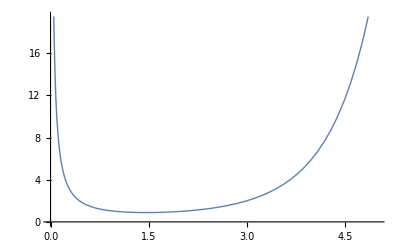

-Graphics3D-

```mathematica
Plot[Gamma[x],{x,0,5},PlotStyle->Thick]
Plot3D[Beta[x,y],{x,0,5},{y,0,5}]
```

Lastnosti funkcij Gama in Beta.

```mathematica
FullSimplify[Gamma[n+1],Assumptions->n∈PositiveIntegers] (*SAMO Z POZITIVNE*)
FullSimplify[Gamma[x+1]==x Gamma[x]]
Gamma[1/2]
FullSimplify[Gamma[x]Gamma[1-x],Assumptions->x>0&&x<1]
%==Pi/Sin[Pi x]
FullSimplify[Beta[x,y]==Gamma[x]Gamma[y]/Gamma[x+y]]
```

n!

True

√π

π Csc[π x]

True

True

# Legendrovi polinomi P_n(x)

Legendrova diferencialna enačba:
(x^2-1)y''+2xy'-n(n+1)y=0

Ena rešitev zgornje Legendrove diferencialne enačbe je polinom
	P_n(x) =∑_(k=0)^N (-1)^k((2 n-2 k)!)/(2^n k! (n-k)! (n-2 k)!)x^(n-2 k),               kjer je   N=Floor[n/2]
V Mathematici  ga zapišemo LegendreP[n,x]. n- STOPNJA POLINOMA

```mathematica
(* Preizkus, da je funkcija y=LegendreP[n,x] res rešitev Legendrove diferencialne enačbe *)
Table[
y=LegendreP[n,x];
Simplify[(x^2-1)D[y,x,x]+2x D[y,x]-n(n+1)y]
,{n,0,10}]
```

{0,0,0,0,0,0,0,0,0,0,0}

Nekaj lastnosti Legendrovih polinomov
P_n(x)  je polinom stopnje n.
P_(2n)(x) je soda funkcija, P_(2n+1)(x) je liha funkcija.
P_n(1)=1 .

{1,x,1/2 (-1+3 x^2),1/2 (-3 x+5 x^3),1/8 (3-30 x^2+35 x^4),1/8 (15 x-70 x^3+63 x^5),1/16 (-5+105 x^2-315 x^4+231 x^6),1/16 (-35 x+315 x^3-693 x^5+429 x^7),1/128 (35-1260 x^2+6930 x^4-12012 x^6+6435 x^8)}

{1,-1,1,-1,1}

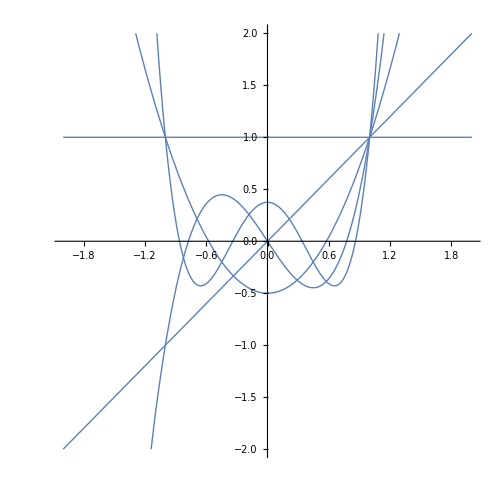

```mathematica
Table[LegendreP[n, x],{n,0,8}]
Table[LegendreP[n, -1],{n,0,4}]
Plot[Table[LegendreP[n, x],{n,0,4}],{x,-2,2},PlotStyle->Thick,ImageSize->500,AspectRatio->Automatic,PlotRange->{-2,2}]
```

Enačba P_n(x)=0  ima n realnih ničel in vse ležijo na intervalu (-1,1).

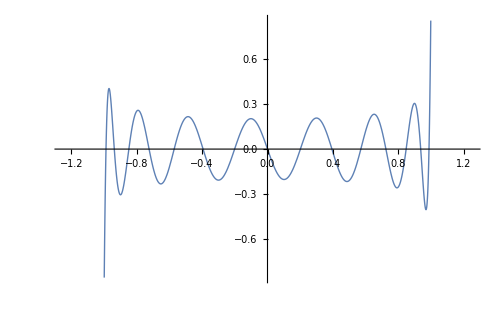

{{x→-0.987993},{x→-0.937273},{x→-0.848207},{x→-0.724418},{x→-0.570972},{x→-0.394151},{x→-0.201194},{x→0.},{x→0.201194},{x→0.394151},{x→0.570972},{x→0.724418},{x→0.848207},{x→0.937273},{x→0.987993}}

```mathematica
MX=1.25;
NP=15;
Plot[LegendreP[NP,x],{x,-MX,MX},PlotStyle->Thick,ImageSize->500]
NSolve[LegendreP[NP,x]==0,x]
```

# Besselove funkcije

Besselova diferencialna enačba
x^2 y''+x y'+(x^2-ν^2)y=0

Ena rešitev zgornje Beselove diferencialne enačbe je Besselova funkcija prve vrste reda ν:
	J_ν(x) =∑_(k=0)^N (-1)^k/(k! Γ(ν+k+1))(x/2)^(ν+2 k) 
V Mathematici  jo zapišemo BesselJ[v,x].

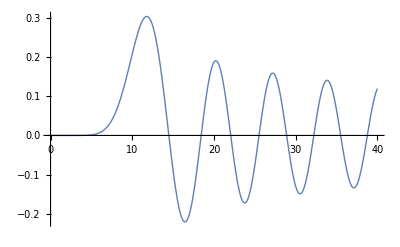

```mathematica
Plot[BesselJ[10,x],{x,0,40},PlotStyle->Thick]
```

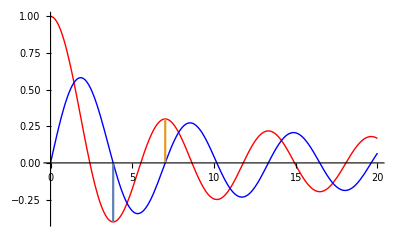

```mathematica
Bes0=Plot[BesselJ[0,x],{x,0,20},PlotStyle->{Thick,Red}];
Bes1=Plot[BesselJ[1,x],{x,0,20},PlotStyle->{Thick,Blue}];
b1=BesselJZero[1,1]; (**)
b2=BesselJZero[1,2];(*1 indeks, 2 druga pozitivna ničla, od modre, 0 odpade*)
crte=ParametricPlot[{{b1,y BesselJ[0,b1]},{b2,y BesselJ[0,b2]}},{y,0,1}];Show[Bes0,Bes1,crte]
```

1. Ničle Besselovih funkcij imajo poseben pomen.
      Ničel posamezne Besselove funkcije je  ∞  mnogo, niso pa enakomerno razporejene!

      Napravite seznam  {α_(k,0),k=1,2,...,9}  prvih 9 ničel funkcije  J_0(x).
      Nato napravite seznam razlik {α_(k+1,0)-α_(k,0),k=1,2,...,9}.
      Koliko se zdi, da je   lim_(k→ ∞) (α_(k+1,0)-α_(k,0))?  PROTI VEDNOSTI Pi!

```mathematica
Solve[BesselJ[0,x]==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-BesselJZero[0,1]}}

```mathematica
FindRoot[BesselJ[0,x],{x,2}]
N[BesselJZero[0,1]] (*posebna funkcija, prva od beslj*)
Table[BesselJ[0,BesselJZero[0,n]],{n,1,4}]

Table[N[BesselJZero[0,n]] , {n,1,9}]
Table[N[BesselJZero[0,n+1]-BesselJZero[0,n]] , {n,1,20}]
```

{x→2.40483}

2.40483

{0,0,0,0}

{2.40483,5.52008,8.65373,11.7915,14.9309,18.0711,21.2116,24.3525,27.4935}

{3.11525,3.13365,3.13781,3.13938,3.14015,3.14057,3.14083,3.14101,3.14113,3.14121,3.14128,3.14133,3.14137,3.1414,3.14142,3.14144,3.14146,3.14147,3.14149,3.1415}

### Primeri nalog za preverjanje

1.Poiščite začetek vrste (do vključno potence  M=6)
                y=∑_(n=0)^∞ c_n x^n,
      ki je rešitev diferencialne enačbe 
                y''-2x y' +y = 0, y(0)=1, y'(0)=-1.    --> To nam pove c0 in c1! 

Rezultat: 1-x-x^2/2-x^3/6-x^4/8-x^5/24-(7 x^6)/240

```mathematica
(* primeri ukazov, ki jih bomo potrebovali *)
Table[n^2,{n,1,4}] (*Tabelira vrednosti*)
Sum[n^2,{n,1,4}] (*sešteje*)
CoefficientList[7+2x-6x^2+4x^4,x] (*vrne koeficiente polinoma*)
Take[%,3] (*za delo s seznami, vzememo le en del. Take, last, first, drop...*)
```

{1,4,9,16}

```mathematica
M=6
y=Sum[c[n] x^n, {n,0,M}]/.c[0]-> 1/.c[1]-> -1
CoefficientList[Simplify[D[y,x,x]-2 x D[y,x] +y],x]
Solve[Take[%,M-1]==0, {c[2], c[3],c[4],c[5],c[6]}]//Flatten
y/.%
```

6

1-x+x^2 c[2]+x^3 c[3]+x^4 c[4]+x^5 c[5]+x^6 c[6]

{1+2 c[2],1+6 c[3],-3 (c[2]-4 c[4]),-5 (c[3]-4 c[5]),-7 c[4]+30 c[6],-9 c[5],-11 c[6]}

{c[2]→-1/2,c[3]→-1/6,c[4]→-1/8,c[5]→-1/24,c[6]→-7/240}

1-x-x^2/2-x^3/6-x^4/8-x^5/24-(7 x^6)/240

```mathematica
M=6;
y=Sum[c[n] x^n,{n,0,M}]/. c[0]-> 1/.c[1]-> -1
Simplify[D[y,x,x]- 2 x D[y,x]+y];
CoefficientList[%,x] (*Dobimo lepo urejene koeficiente*)
Solve[%==0,{c[2],c[3],c[4],c[5],c[6]}](*Zadnji dve enečbi nista več ok saj ni c7... vzememo malomanj*)
Solve[Take[%%,M-1]==0,Table[c[n],{n,2,M}]] //Flatten
y/.%
```

1-x+x^2 c[2]+x^3 c[3]+x^4 c[4]+x^5 c[5]+x^6 c[6]

{1+2 c[2],1+6 c[3],-3 (c[2]-4 c[4]),-5 (c[3]-4 c[5]),-7 c[4]+30 c[6],-9 c[5],-11 c[6]}

{}

{c[2]→-1/2,c[3]→-1/6,c[4]→-1/8,c[5]→-1/24,c[6]→-7/240}

1-x-x^2/2-x^3/6-x^4/8-x^5/24-(7 x^6)/240

2.Poiščite začetek vrste (do vključno potence  M=6)
                y=∑_(n=0)^∞ c_n x^n,
      ki je rešitev diferencialne enačbe 
                xy''+ y' -xy = 0, y(0)=36, y'(0)=0.

Rezultat: 36+9 x^2+(9 x^4)/16+x^6/64

```mathematica
M=6;
y=Sum[c[n] x^n,{n,0,M}]/. c[0]-> 36/.c[1]-> 0
Simplify[x D[y,x,x]+   D[y,x]-x y];
CoefficientList[%,x] (*Dobimo lepo urejene koeficiente*)
(*Zadnji dve enečbi nista več ok saj ni c7... vzememo prvih 6 -> pet enačb pet neznank + 0*)
Solve[Take[%,M]==0,Table[c[n],{n,2,M}]] //Flatten
y/.%
```

36+x^2 c[2]+x^3 c[3]+x^4 c[4]+x^5 c[5]+x^6 c[6]

{0,-36+4 c[2],9 c[3],-c[2]+16 c[4],-c[3]+25 c[5],-c[4]+36 c[6],-c[5],-c[6]}

{c[2]→9,c[3]→0,c[4]→9/16,c[5]→0,c[6]→1/64}

36+9 x^2+(9 x^4)/16+x^6/64

```mathematica
(***************************************************************************)
Clear[y,x]
DSolve[{x y''[x]+y'[x]-x y[x]==0,y[0]==36, y'[0]==0},y[x],x]//Flatten
Series[y[x]/.%,{x,0,6}]
```

{y[x]→36 BesselJ[0,ⅈ x]}

36+9 x^2+(9 x^4)/16+x^6/64+O[x]^7

3.Poiščite začetek vrste (do vključno potence  M=6)
                y=x^r∑_(n=0)^∞ c_n x ^n ,
      ki je rešitev diferencialne enačbe 
                (x^2+x)y''- (x^2-2)y' -(x+2)y = 0.

Rezultat: A/x+B+B x+(B x^2)/2+(B x^3)/6+(B x^4)/24+(B x^5)/120+(B x^6)/720

```mathematica
y=Sum[c[n] x^(n+r),{n,0,M}]
de=(x^2 +x)D[y,x,x]- (x^2 -2)D[y,x]-(x+2)y //Expand
CoefficientList[de,x];
Coefficient[de,x^{r-1}]
Solve[%==0,r]
```

x^r c[0]+x^(1+r) c[1]+x^(2+r) c[2]+x^(3+r) c[3]+x^(4+r) c[4]+x^(5+r) c[5]+x^(6+r) c[6]

r x^(-1+r) c[0]+r^2 x^(-1+r) c[0]-2 x^r c[0]-r x^r c[0]+r^2 x^r c[0]-x^(1+r) c[0]-r x^(1+r) c[0]+2 x^r c[1]+3 r x^r c[1]+r^2 x^r c[1]-2 x^(1+r) c[1]+r x^(1+r) c[1]+r^2 x^(1+r) c[1]-2 x^(2+r) c[1]-r x^(2+r) c[1]+6 x^(1+r) c[2]+5 r x^(1+r) c[2]+r^2 x^(1+r) c[2]+3 r x^(2+r) c[2]+r^2 x^(2+r) c[2]-3 x^(3+r) c[2]-r x^(3+r) c[2]+12 x^(2+r) c[3]+7 r x^(2+r) c[3]+r^2 x^(2+r) c[3]+4 x^(3+r) c[3]+5 r x^(3+r) c[3]+r^2 x^(3+r) c[3]-4 x^(4+r) c[3]-r x^(4+r) c[3]+20 x^(3+r) c[4]+9 r x^(3+r) c[4]+r^2 x^(3+r) c[4]+10 x^(4+r) c[4]+7 r x^(4+r) c[4]+r^2 x^(4+r) c[4]-5 x^(5+r) c[4]-r x^(5+r) c[4]+30 x^(4+r) c[5]+11 r x^(4+r) c[5]+r^2 x^(4+r) c[5]+18 x^(5+r) c[5]+9 r x^(5+r) c[5]+r^2 x^(5+r) c[5]-6 x^(6+r) c[5]-r x^(6+r) c[5]+42 x^(5+r) c[6]+13 r x^(5+r) c[6]+r^2 x^(5+r) c[6]+28 x^(6+r) c[6]+11 r x^(6+r) c[6]+r^2 x^(6+r) c[6]-7 x^(7+r) c[6]-r x^(7+r) c[6]

{r c[0]+r^2 c[0]}

{{r→-1},{r→0}}

```mathematica
r=-1;
(*n+r=M=6-r*)
M=6-r;
y=Sum[c[n] x^(n+r),{n,0,M}]
Simplify[(x^2 +x)D[y,x,x]- (x^2 -2)D[y,x]-(x+2)y ];
CoefficientList[%,x]
Solve[Take[%,M]==0,Table[c[n],{n,1,M}]] //Flatten
y1=y/.%/.c[0]-> A
```

c[0]/x+c[1]+x c[2]+x^2 c[3]+x^3 c[4]+x^4 c[5]+x^5 c[6]+x^6 c[7]

{-2 c[1]+2 c[2],-c[1]-2 c[2]+6 c[3],-2 c[2]+12 c[4],-3 c[3]+4 c[4]+20 c[5],-4 c[4]+10 c[5]+30 c[6],-5 c[5]+18 c[6]+42 c[7],-6 c[6]+28 c[7],-7 c[7]}

{c[1]→0,c[2]→0,c[3]→0,c[4]→0,c[5]→0,c[6]→0,c[7]→0}

A/x

```mathematica
r=0;
(*n+r=M=6-r*)
M=6-r;
y=Sum[c[n] x^(n+r),{n,0,M}]
Simplify[(x^2 +x)D[y,x,x]- (x^2 -2)D[y,x]-(x+2)y ];
CoefficientList[%,x]
Solve[Take[%,M]==0,Table[c[n],{n,1,M}]] //Flatten
y2=y/.%/.c[0]-> B
```

c[0]+x c[1]+x^2 c[2]+x^3 c[3]+x^4 c[4]+x^5 c[5]+x^6 c[6]

{-2 c[0]+2 c[1],-c[0]-2 c[1]+6 c[2],-2 c[1]+12 c[3],-3 c[2]+4 c[3]+20 c[4],-4 c[3]+10 c[4]+30 c[5],-5 c[4]+18 c[5]+42 c[6],-6 c[5]+28 c[6],-7 c[6]}

{c[1]→c[0],c[2]→c[0]/2,c[3]→c[0]/6,c[4]→c[0]/24,c[5]→c[0]/120,c[6]→c[0]/720}

B+B x+(B x^2)/2+(B x^3)/6+(B x^4)/24+(B x^5)/120+(B x^6)/720

```mathematica
y=y1+y2
```

B+A/x+B x+(B x^2)/2+(B x^3)/6+(B x^4)/24+(B x^5)/120+(B x^6)/720

```mathematica
(*koraki:
1. Določimo rje, da ugotovimo s čim moramo deliti da odpravimo singularnost. Kdaj je koeficient = 0
2.  dobimo dve različni konstanti
3. oboje seštejemo*)
```

4. S povezavo y=z/x^2 vpeljite v diferencialno enačbo
                (x^4-x^2)y''+(6 x^3-4x) y'-(24 x^2+2)y=0
      novo neznano funkcijo z(x).
      Ena rešitev nastale enačbe je Legendrov polinom  z=P_n(x).
      Koliko je vrednost tega polinoma P_n(x) v x=2?

Rezultat: 185.75

Legendrova diferencialna enačba:
(x^2-1)y''+2xy'-n(n+1)y=0

```mathematica
Clear[x,y,z]
y[x_]:=z[x]/x^2
Simplify[(x^4 -x^2) y''[x]+(6x^3-4x)y'[x]-(24x^2+2)y[x]==0]
LegendreP[5,2]//N
```

30 z[x]==2 x z'[x]+(-1+x^2) z''[x]

185.75

```mathematica
(****************************************************************)
y=z[x]/x^2
Simplify[(x^4 -x^2) D[y,x,x]+(6x^3-4x)D[y,x]-(24x^2+2)y==0]
```

z[x]/x^2

30 z[x]==2 x z'[x]+(-1+x^2) z''[x]

5. S povezavo y=x^3 z    vpeljite v diferencialno enačbo
                x^2 y''-5x y'+(x^2-40)y=0
      novo neznano funkcijo z(x).
      Ena rešitev nastale enačbe je Besselova funkcija prve vrste  z=J_n(x).
      Koliko je  13-ta  pozitivna ničla te funkcije?

Rezultat:50.5682

Besselova diferencialna enačba
x^2 y''+x y'+(x^2-ν^2)y=0

```mathematica
Clear[x,y,z]
y[x_]:=x^3 z[x]
Simplify[((x^2  y''[x]-5x y'[x]+(x^2-40)y[x])/x^3)==0]
BesselJZero[7,13]//N (*7 prepoznamo iz oblike*)
```

(-49+x^2) z[x]+x (z'[x]+x z''[x])==0

50.5682

6.Z vpeljavo nove neodvisne spremenljivke t=x^2 poiščite eno rešitev diferencialne enačbe
                (x^2-1/x^2)(y''-y'/x)+4x y'-48y=0.
      Izračunajte y_1(5).

Rezultat:305

```mathematica
Clear[x,y,z,Y]
Y[x_]:=y[x^2] (*t=x^2*)
Simplify[((x^2-1/x^2)(y''[x]-y'[x]/ x)+ 4x y'[x]- 48 y[x]==0 )/. y-> Y /. x-> Sqrt[t]]
LegendreP[3,5]
```

12 y[t]==2 t y'[t]+(-1+t^2) y''[t]

305

7. S substitucijama t=x^3 in y=z/x prevedite diferencialno enačbo
               xy''+3y'+9 x^5 y=0
      do Besselove diferencialne enačbe z eno izmed rešitev z=J_ν(t).
      Koliko je J_ν(1) za pozitiven dobljen ν?

Rezultat: 0.730876

```mathematica
Clear[x,y,z,Y];
y[x_]:=z[x]/x
Y[x_]:=z[x^3] (*t=x^3*)


Simplify[(x y''[x]+3 y'[x]+ 9x^5 y[x]==0) /.z-> Y /. x-> CubeRoot[t]]
Simplify[((x y''[x]+3 y'[x]+ 9x^5 y[x]) *CubeRoot[t]^2 /9==0) /.z-> Y /. x-> CubeRoot[t]]
BesselJ[1/3,1]//N
```

((-1+9 t^2) z[t]+9 t (z'[t]+t z''[t]))/t^(1/3)==0

(-1/9+t^2) z[t]+t (z'[t]+t z''[t])==0

0.730876